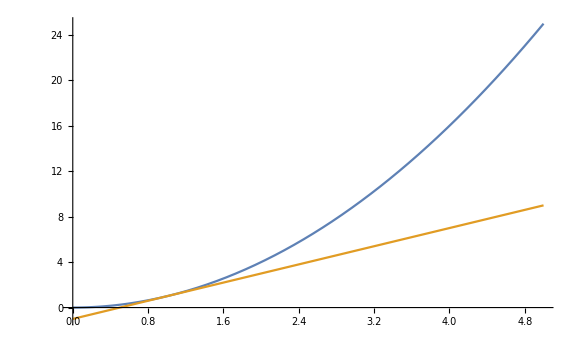

```mathematica
(*Function with a tangent line*)
Plot[{x^2,2(x-1)+1,(q[t]^2-1)(x-1)/(q[t]-1)+1},{x,0,5},ImageSize->Large]
```

```mathematica
(*Secant lines with h->0*)
 q[t_]=q[t_]=4(1-t)+a;
f[x_]=x^2;
a=1;
Manipulate[Show[{Plot[{f[x],(f[q[t]]-a)(x-a)/(q[t]-1)+f[a]},{x,0,5}],ListPlot[{{a,f[a]},{q[t],f[q[t]]}},PlotStyle->PointSize[.013]] },{PlotRange-> {-5,25},ImageSize->Large}],{t,0,.999999}]
```

```mathematica
(*same, now with tangent line drawn in*)
 q[t_]=4(1-t)+a;
f[x_]=x^2;
a=1;
Manipulate[Show[{Plot[{f[x],f'[a](x-a)+f[a],(f[q[t]]-a)(x-a)/(q[t]-1)+f[a]},{x,0,5}],ListPlot[{{a,f[a]},{q[t],f[q[t]]}},PlotStyle->PointSize[.013]] },{PlotRange-> {-5,25},ImageSize->Large}],{t,0,.999999}]
```

```mathematica
Quit
```

```mathematica
(*zooming in on a function to demonstrate linear approximation by tangents, first w/o actual tangent line, then with--CF def of derivative*)
g[x_]=Sin[x];
a=Pi/2+.1;
u[t_]=10^(.3-3.5t);
Manipulate[Show[Plot[g[x],{x,a-u[t],a+u[t]}],ListPlot[{{a,g[a]}},PlotStyle->PointSize[.025]],ImageSize->Large],{t,0,1}]
(*Manipulate[Show[Plot[{g[x],((g[a+u[t]]-g[a])/(u[t]))(x-a)+g[a]},{x,a-u[t]/10,a+u[t]}],ListPlot[{{a,g[a]}},PlotStyle->PointSize[.025]],ImageSize->Large],{t,0,1}]*)
Manipulate[Show[Plot[{g[x],g'[a](x-a)+g[a]},{x,a-u[t],a+u[t]}],ListPlot[{{a,g[a]}},PlotStyle->PointSize[.025]],ImageSize->Large],{t,0,1}]
```

```mathematica
Quit
```

```mathematica
(*What if the function is not differentiable? [version 1]*)
a=Pi/2-.1;
(*b=a+.001;*)
(*g[x_]=2-((x-a)^2)^(1/3);*)
h[x_]=Piecewise[{{(3/2)x^2-x,x<a},{(3/2)x^2+3x-4a,x≥ a}}];
u[t_]=10^(.5-5t);
Manipulate[Show[Plot[h[x],{x,a-u[t],a+u[t]}],ListPlot[{{a,h[a]}},PlotStyle->PointSize[.025]],ImageSize->Large],{t,0,1}]
(*Manipulate[Show[Plot[g[x],{x,a-u[t],a+u[t]}],ImageSize->Large],{t,0,1}]*)
(*Manipulate[Show[Plot[g[x],{x,b-u[t],b+u[t]}],ListPlot[{{b,g[b]}},PlotStyle->PointSize[.025]],ImageSize->Large],{t,0,1}]*)
(*Manipulate[Show[Plot[{g[x],g'[a](x-a)+g[a]},{x,a-u[t],a+u[t]}],ListPlot[{{a,g[a]}},PlotStyle->PointSize[.025]],ImageSize->Large],{t,0,1}]*)
```

```mathematica
Quit
```

```mathematica
(*What if the function is not differentiable? [version 2]*)
a=Pi/2-.1;
b=a+.001;
g[x_]=2-((x-a)^2)^(1/3);
(*h[x_]=Integrate[3t+(t-a)/Abs[t-a],{t,0,x}];*)
u[t_]=10^(.5-5t);
(*Manipulate[Show[Plot[h[x],{x,a-u[t],a+u[t]}],ListPlot[{{a,h[a]}},PlotStyle->PointSize[.025]],ImageSize->Large],{t,0,1}]*)
Manipulate[Show[Plot[g[x],{x,a-u[t],a+u[t]}],ImageSize->Large],{t,0,1}]
Manipulate[Show[Plot[g[x],{x,b-u[t],b+u[t]}],ListPlot[{{b,g[b]}},PlotStyle->PointSize[.025]],ImageSize->Large],{t,0,1}]
(*Manipulate[Show[Plot[{g[x],g'[a](x-a)+g[a]},{x,a-u[t],a+u[t]}],ListPlot[{{a,g[a]}},PlotStyle->PointSize[.025]],ImageSize->Large],{t,0,1}]*)
```

```mathematica
Quit
```

```mathematica
(*What about [continuous] functions which are nowhere differentiable? answer: it gets really weird*)
W[x_]=Sum[(1/2)^n*Cos[3^n*Pi*x],{n,0,100}];
a=Pi/2-.1;
u[t_]=10^(.5-8t);
Manipulate[Show[Plot[W[x],{x,a-u[t],a+u[t]}],ListPlot[{{a,W[a]}},PlotStyle->PointSize[.025]],ImageSize->Large],{t,0,1}]
```

```mathematica
Quit
```

```mathematica
(*also tangent line approximation doesn't work*) 
a=438/927;
q[t_]= E^(Log[.5-a]-8 t)+a;
f[x_]=Sum[(1/2)^n*Cos[3^n*Pi*x],{n,0,15}];
Manipulate[Show[{Plot[{f[x],(f[q[t]]-f[a])(x-a)/(q[t]-a)+f[a]},{x,q[1]-(q[0]-q[1])/4,q[0]}],ListPlot[{{a,f[a]},{q[t],f[q[t]]}},PlotStyle->PointSize[.013]] },{PlotRange-> {-.2,.2},ImageSize->Large}],{t,0,.999999}]
```